# Combine Plots

## LEP experiment 1996

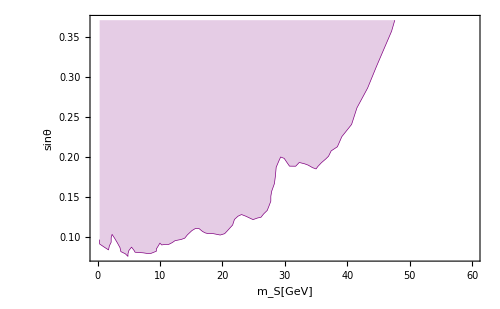

```mathematica
LEP1996data={#1,√#2}&@@@Import[NotebookDirectory[]<>"/probe/LEP1996.csv"];
LEP1996=ListLinePlot[LEP1996data,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[Purple,Thickness[0.001]]]
```

## LHCb experiment

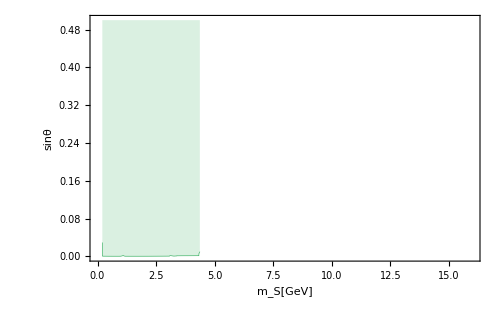

```mathematica
LHCbdata={#1, √#2}& @@@Import[NotebookDirectory[]<>"probe/LHCb.csv"];
LHCb=ListLinePlot[LHCbdata,Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[GeV]",FontFamily->"Times",FontSize->18],Style["sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,ImageSize->500,PlotStyle->Directive[ColorData[97,15],Thickness[0.001]],PlotRange->{{0,16},{0,0.5}}]
```

## Exotic Decay

```mathematica
v=246.22;
mhpole=125.13;
ΓSM=4.07*10^-3;(*GeV*)
A[mS_,sinθ_]:=((mhpole^2-mS^2)sinθ √(1-sinθ^2))/v;
λhL[mS_,sinθ_]:=((1-sinθ^2)mhpole^2+sinθ^2 mS^2)/(2 v^2);
ghSS[mS_,sinθ_]:=-1/4 A[mS,sinθ]sinθ(1+3(1-2 sinθ^2))+3λhL[mS,sinθ]v sinθ^2 √(1-sinθ^2);
ΓhSS[mS_,sinθ_]:=ghSS[mS,sinθ]^2/(32π mhpole)√(1-4 mS^2/mhpole^2);
BRhSS[mS_,sinθ_]:=ΓhSS[mS,sinθ]/(ΓSM+ΓhSS[mS,sinθ]);
```

```mathematica
prospectdata=Import[NotebookDirectory[]<>"probe/Exoticdecay.csv"];
prospectfunc[mS_]:=Interpolation[prospectdata][mS];
Currentdata1=Import[NotebookDirectory[]<>"probe/ExoticDecayCurrent1.csv"];
Currentdata2=Import[NotebookDirectory[]<>"probe/ExoticDecayCurrent2.csv"];
Higgsfactorydata=Import[NotebookDirectory[]<>"probe/Higgsfactory.csv"];
Higgsfactoryfunc[mS_]:=Interpolation[Higgsfactorydata][mS]
Higgsfactorydata2=Import[NotebookDirectory[]<>"probe/Higgsfactory02.csv"];
Higgsfactoryfunc2[mS_]:=Interpolation[Higgsfactorydata2][mS]
Currentfunc1[mS_]:=Interpolation[Currentdata1][mS];
Currentfunc2[mS_]:=Interpolation[Currentdata2][mS];
```

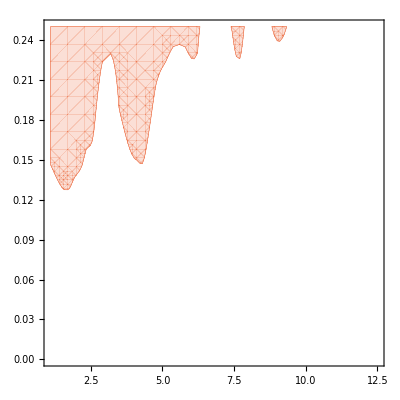

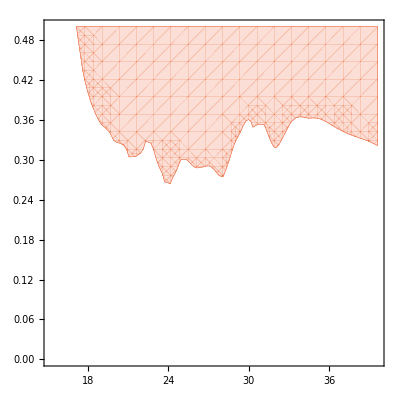

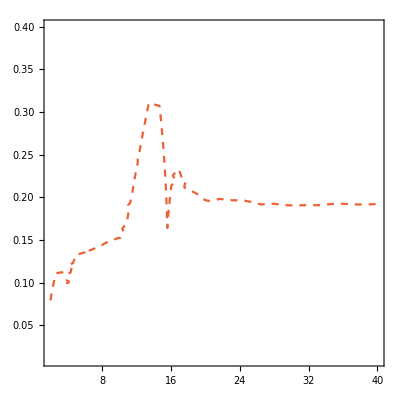

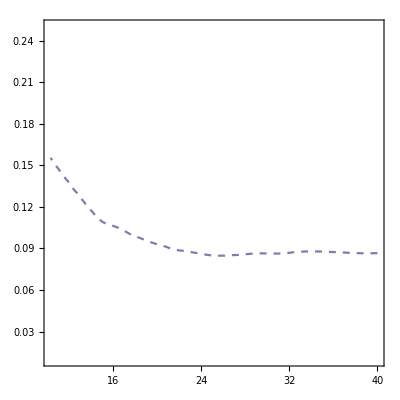

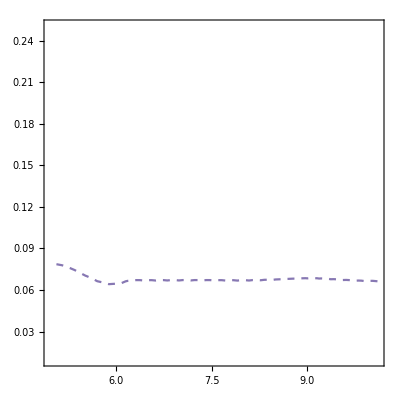

```mathematica
exotic1=RegionPlot[BRhSS[mS,sinθ]>=Currentfunc1[mS],{mS,1.1,12.5},{sinθ,0,0.25},PlotStyle->Directive[Opacity[0.2],ColorData[97,4]],BoundaryStyle->Directive[Thickness[0.001],ColorData[97,4]]]
exotic2=RegionPlot[BRhSS[mS,sinθ]>=Currentfunc2[mS],{mS,15.2,39.6},{sinθ,0,0.5},PlotStyle->Directive[Opacity[0.2],ColorData[97,4]],BoundaryStyle->Directive[Thickness[0.001],ColorData[97,4]]]
exoticprosp=ContourPlot[BRhSS[mS,sinθ]==prospectfunc[mS],{mS,2,40},{sinθ,0.01,0.4},ContourStyle->Directive[Dashed,ColorData[97,4]]]
Higgsfactory=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc[mS],{mS,10.3,40},{sinθ,0.01,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]]
Higgsfactory2=ContourPlot[BRhSS[mS,sinθ]==Higgsfactoryfunc2[mS],{mS,4.97,10.1},{sinθ,0.01,0.25},ContourStyle->Directive[Dashed,ColorData[97,5]]]
```

## Kaon decay

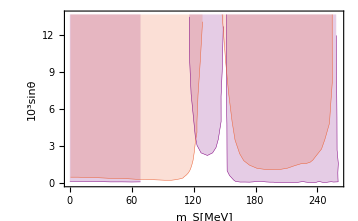

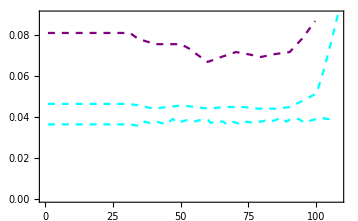

```mathematica
NA621={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-1.csv"];
NA622={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-2.csv"];
NA623={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/NA62-3.csv"];
E9491={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949.csv"];
E9492={#1,1000*√(#2/(1.7*10^-3))}& @@@Import[NotebookDirectory[]<>"./probe/E949-2.csv"];
NA62‵run2={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/NA62-run2.csv"];
HIKE1={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/HIKE-1.csv"];
HIKE2={#1*1000,1000*√#2}&@@@Import[NotebookDirectory[]<>"./probe/HIKE-2.csv"];
Kaondecay1=ListLinePlot[{NA621,NA622,NA623,E9491,E9492},Filling->Top,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotStyle->{Directive[Purple,Thickness[0.001]],Directive[Purple,Thickness[0.001]],Directive[Purple,Thickness[0.001]],Directive[ColorData[97,4],Thickness[0.001]],Directive[ColorData[97,4],Thickness[0.001]]}]
Kaondecay2=ListLinePlot[{NA62‵run2,HIKE1,HIKE2},PlotStyle->{Directive[Dashed,Purple],Directive[Dashed,Cyan],Directive[Dashed,Cyan]}]
```

## CMB probe

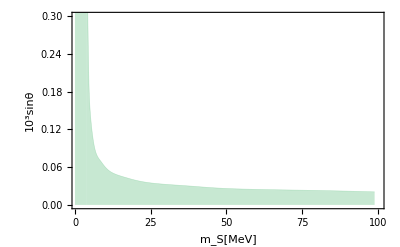

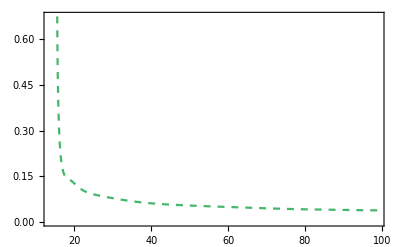

```mathematica
CMBS4data={#1,1000#2}&@@@Import[NotebookDirectory[]<>"./probe/CMB-S4.csv"];
CMBfunc[mS_]:=Interpolation[CMBS4data][mS]
perspect‵CMB‵data=SortBy[{#1,1000#2}&@@@Import[NotebookDirectory[]<>"./probe/CMB-perspective.csv"],First];
Planck01=Plot[y=10,{x,0,Min[{#1}&@@@CMBS4data]},Filling->Bottom,PlotStyle->{ColorData[97,15],Opacity[0.3]},FillingStyle->Opacity[0.3]];
Planck02=ListLinePlot[CMBS4data,PlotRange->Full,InterpolationOrder->3,AxesOrigin->{1,0.},Filling->Bottom,BaseStyle->{FontSize->16,FontFamily->"Times"},Frame->True,FrameLabel->{Style["m_S[MeV]",FontFamily->"Times",FontSize->18],Style["10^3sinθ",FontFamily->"Times",FontSize->18]},LabelStyle->{Black},FrameTicksStyle->{Directive[FontFamily->"Times",FontSize->18]},PlotRangePadding->None,PlotStyle->{ColorData[97,15],Opacity[0.3],Thickness[0.001]},FillingStyle->Opacity[0.3]];
Planck=Show[Planck02,Planck01,PlotRange->{{1,100},{0,0.3}}]
CMB‵perspect=ListLinePlot[perspect‵CMB‵data,InterpolationOrder->3,PlotRange->Full,PlotStyle->Directive[Dashed,ColorData[97,15]]]
```

## Supernovae

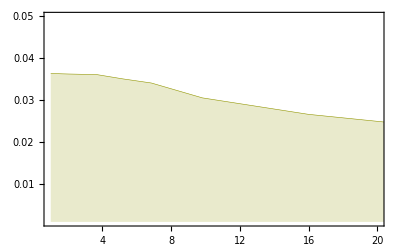

```mathematica
SNdata={#1,1000*#2}&@@@Import[NotebookDirectory[]<>"probe/SN.csv"];
SN=ListLinePlot[SNdata,Filling->Bottom,PlotStyle->{Directive[Thickness[0.001],ColorData[97,10]]},PlotRange->{{1,20},{0.001,0.05}}]
```

## SFOPT bound

### GeV scale

```mathematica
c100‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c100_delta_2pi5_GeV_out.csv"];
c100‵δ2pi5‵strength‵data={#1,#2,#10}&@@@c100‵δ2pi5‵data;
c30‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_2pi5_GeV_out.csv"];
c30‵δ2pi5‵strength‵data={#1,#2,#10}&@@@c30‵δ2pi5‵data;
c3‵δ2pi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_2pi5_GeV_out.csv"];
c3‵δ2pi5‵strength‵data={#1,#2,#10}&@@@Select[c3‵δ2pi5‵data,Length[#]>10 &];
c30‵δpi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_pi5_GeV_out.csv"];
c30‵δpi5‵strength‵data={#1,#2,1.2*#8}&@@@c30‵δpi5‵data;
c3‵δpi5‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_pi5_GeV_out.csv"];
c3‵δpi5‵strength‵data={#1,#2,1.2*#8}&@@@c3‵δpi5‵data;
c12‵δpi20‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c12_delta_pi20_GeV_out.csv"];
c12‵δpi20‵strength‵data={#1,#2,1.2*#8}&@@@c12‵δpi20‵data;
c15‵δpi20‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c15_delta_pi20_GeV_out.csv"];
c15‵δpi20‵strength‵data={#1,#2,1.2*#8}&@@@c15‵δpi20‵data;
```

Discuss some naturalness requirement here:

```mathematica
c3‵δ2pi5‵natural‵data={#1,#2,√((16 π^2#6 #7)/#4)}&@@@c3‵δ2pi5‵data;
c3‵δpi5‵natural‵data={#1,#2,√((16 π^2#6 #7)/#4)}&@@@c3‵δpi5‵data;
```

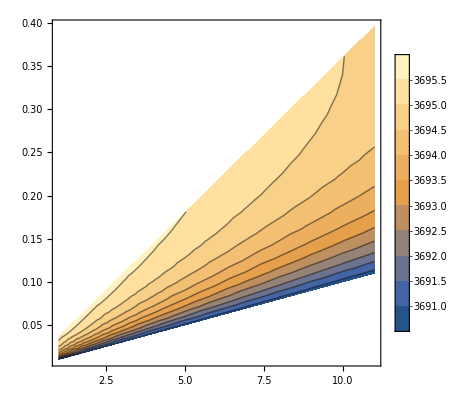

```mathematica
ListContourPlot[c3‵δ2pi5‵natural‵data,PlotLegends->Automatic]
```

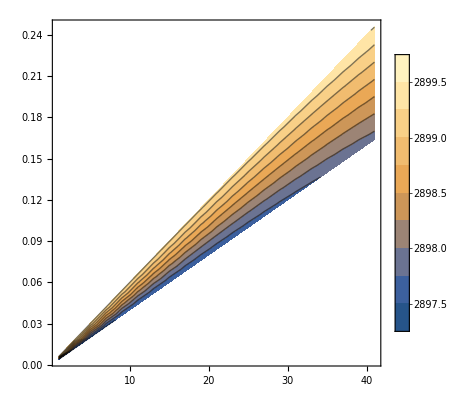

```mathematica
ListContourPlot[c3‵δpi5‵natural‵data,PlotLegends->Automatic]
```

```mathematica
c100‵δ2pi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c100‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.05],PlotRange->Full];
c30‵δ2pi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c3‵δ2pi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δ2pi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.3],PlotRange->Full];
c3‵δpi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δpi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.3],PlotRange->Full];
c30‵δpi5‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δpi5‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c12‵δpi20‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c12‵δpi20‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.3],PlotRange->Full];
c15‵δpi20‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c15‵δpi20‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
```

```mathematica
TnTcratiodata={#10/#8}&@@@Select[Select[c3‵δ2pi5‵data,(Length[#]>10 )&],1.3>#[[10]]>0.8 &]//Flatten;
```

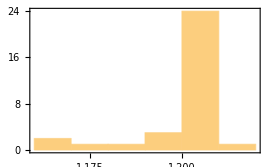

```mathematica
Histogram[TnTcratiodata]
```

```mathematica
Mean[TnTcratiodata]
```

1.20016

## MeV

```mathematica
c100‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c100_delta_2pi5_MeV_out.csv"];
c100‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c100‵δ2pi5‵MeV‵data;
c30‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_2pi5_MeV_out.csv"];
c30‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c30‵δ2pi5‵MeV‵data;
c3‵δ2pi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_2pi5_MeV_out.csv"];
c3‵δ2pi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c3‵δ2pi5‵MeV‵data;
c3‵δpi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c3_delta_pi5_MeV_out.csv"];
c3‵δpi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c3‵δpi5‵MeV‵data;
c30‵δpi5‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c30_delta_pi5_MeV_out.csv"];
c30‵δpi5‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c30‵δpi5‵MeV‵data;
c12‵δpi20‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c12_delta_pi20_MeV_out.csv"];
c12‵δpi20‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c12‵δpi20‵MeV‵data;
c15‵δpi20‵MeV‵data=Import[NotebookDirectory[]<>"/phase_transition/output/c15_delta_pi20_MeV_out.csv"];
c15‵δpi20‵MeV‵strength‵data={#1*1000,#2*1000,1.2*#8}&@@@c15‵δpi20‵MeV‵data;
```

```mathematica
c100‵δ2pi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c100‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.05],PlotRange->Full];
c30‵δ2pi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c3‵δ2pi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δ2pi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.2],PlotRange->Full,InterpolationOrder->3];
c30‵δpi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c30‵δpi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
c3‵δpi5‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c3‵δpi5‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.2],PlotRange->Full];
c12‵δpi20‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c12‵δpi20‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.2],PlotRange->Full];
c15‵δpi20‵MeV‵strength‵plot=ListLinePlot[Cases[ListContourPlot[c15‵δpi20‵MeV‵strength‵data,Contours->{1.0},ContourShading->None,PlotRange->Full][[1]]//Normal,Line[z_]->z,Infinity],Filling->Bottom,FillingStyle->Opacity[0.1],PlotRange->Full];
```

## Combine

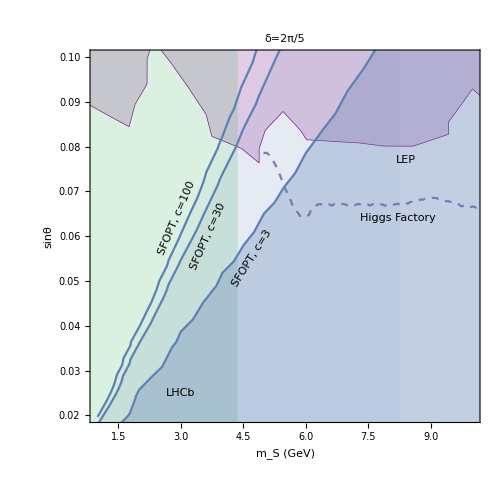

```mathematica
Show[LEP1996,LHCb,Higgsfactory,Higgsfactory2,c100‵δ2pi5‵strength‵plot,c30‵δ2pi5‵strength‵plot,c3‵δ2pi5‵strength‵plot,PlotRange->{{1,10},{0.02,0.1}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=2π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Rotate[Framed[Style["SFOPT, c=3",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],58 Degree],{4.7,0.055}],Inset[Rotate[Framed[Style["SFOPT, c=30",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],66 Degree],{3.65,0.06}],Inset[Rotate[Framed[Style["SFOPT, c=100",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],67 Degree],{2.9,0.064}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{8.2,0.064}],Inset[Rotate[Framed[Style["LEP",Purple,FontSize->22],FrameStyle->None],0Degree],{8.4,0.077}],Inset[Rotate[Framed[Style["LHCb",ColorData[97,15],FontSize->22],FrameStyle->None],0Degree],{3,0.025}]}]
```

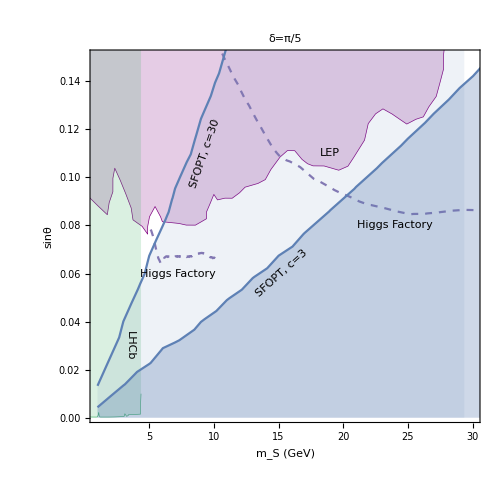

```mathematica
Show[LEP1996,LHCb,Higgsfactory,Higgsfactory2,c3‵δpi5‵strength‵plot,c30‵δpi5‵strength‵plot,PlotRange->{{1,30},{0.001,0.15}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Rotate[Framed[Style["SFOPT, c=3",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],42 Degree],{15.2,0.06}],Inset[Rotate[Framed[Style["SFOPT, c=30",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],71 Degree],{9.3,0.11}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{24,0.08}],
Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{7.2,0.06}],Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->22,Purple],FrameStyle->None],{19,0.11}],Inset[Rotate[Framed[Style["LHCb",ColorData[97,15],FontSize->22],FrameStyle->None],-90Degree],{3.5,0.03}]}]
```

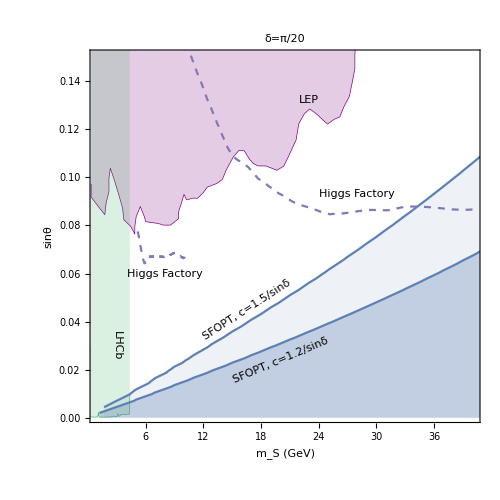

```mathematica
Show[LEP1996,LHCb,Higgsfactory,Higgsfactory2,c12‵δpi20‵strength‵plot,c15‵δpi20‵strength‵plot,PlotRange->{{1,40},{0.001,0.15}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (GeV)",FontFamily->"Times",FontSize->24],Style["sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/20",FontFamily->"Times",FontSize->26],Epilog->{Inset[Rotate[Framed[Style["SFOPT, c=1.2/sinδ",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],23 Degree],{20,0.024}],Inset[Rotate[Framed[Style["SFOPT, c=1.5/sinδ",FontFamily->"Times",FontSize->24,FontColor->ColorData[97,1]],FrameStyle->None],33 Degree],{16.5,0.045}],Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{28,0.093}],
Inset[Rotate[Framed[Style["Higgs Factory",ColorData[97,5],FontSize->22],FrameStyle->None],0Degree],{8,0.06}],Inset[Framed[Style["LEP",FontFamily->"Times",FontSize->22,Purple],FrameStyle->None],{23,0.132}],Inset[Rotate[Framed[Style["LHCb",ColorData[97,15],FontSize->22],FrameStyle->None],-90Degree],{3,0.03}]}]
```

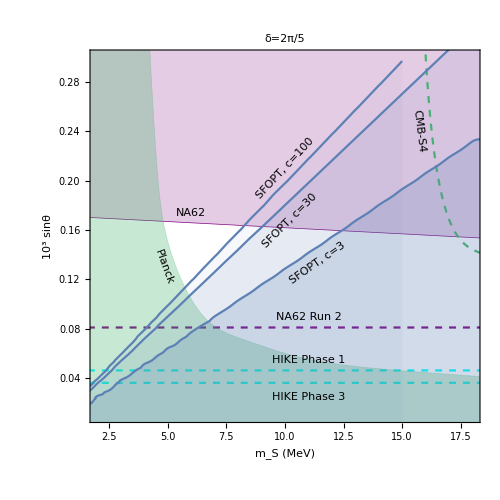

```mathematica
Show[Kaondecay1,Kaondecay2,CMB‵perspect,Planck,c100‵δ2pi5‵MeV‵strength‵plot,c30‵δ2pi5‵MeV‵strength‵plot,c3‵δ2pi5‵MeV‵strength‵plot,PlotRange->{{2,18},{0.01,0.3}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=2π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Framed[Style["NA62",Purple, FontFamily->"Times",FontSize->24],FrameStyle->None],{6,0.174}],Inset[Rotate[Framed[Style["Planck",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-70 Degree],{4.85,0.13}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-83Degree],{15.7,0.24}],Inset[Rotate[Framed[Style["NA62 Run 2",Purple,FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{11,0.09}],Inset[Rotate[Framed[Style["HIKE Phase 1",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{11,0.055}],Inset[Rotate[Framed[Style["HIKE Phase 3",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{11,0.025}],Inset[Rotate[Framed[Style["SFOPT, c=3",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],35Degree],{11.4,0.133}],Inset[Rotate[Framed[Style["SFOPT, c=30",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],45Degree],{10.2,0.168}],Inset[Rotate[Framed[Style["SFOPT, c=100",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],47Degree],{10,0.21}]}]
```

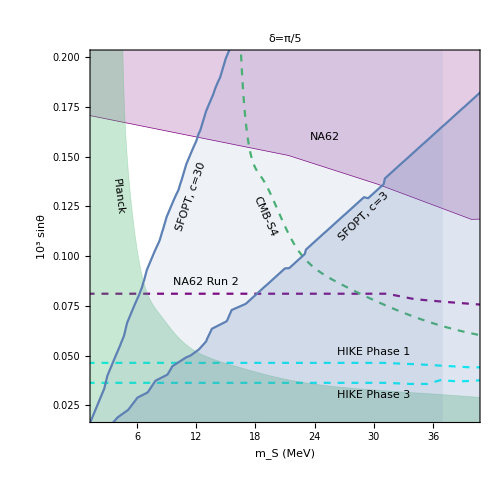

```mathematica
Show[Kaondecay1,Kaondecay2,CMB‵perspect,Planck,c3‵δpi5‵MeV‵strength‵plot,c30‵δpi5‵MeV‵strength‵plot,PlotRange->{{2,40},{0.02,0.2}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/5",FontFamily->"Times",FontSize->26],Epilog->{Inset[Framed[Style["NA62",Purple, FontFamily->"Times",FontSize->24],FrameStyle->None],{25,0.16}],Inset[Rotate[Framed[Style["SFOPT, c=3",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],44Degree],{29,0.12}],Inset[Rotate[Framed[Style["SFOPT, c=30",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],71Degree],{11.5,0.13}],Inset[Rotate[Framed[Style["Planck",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-83 Degree],{4.1,0.13}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-66Degree],{19,0.12}],Inset[Rotate[Framed[Style["NA62 Run 2",Purple,FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{13,0.087}],Inset[Rotate[Framed[Style["HIKE Phase 1",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{30,0.052}],Inset[Rotate[Framed[Style["HIKE Phase 3",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{30,0.030}]}]
```

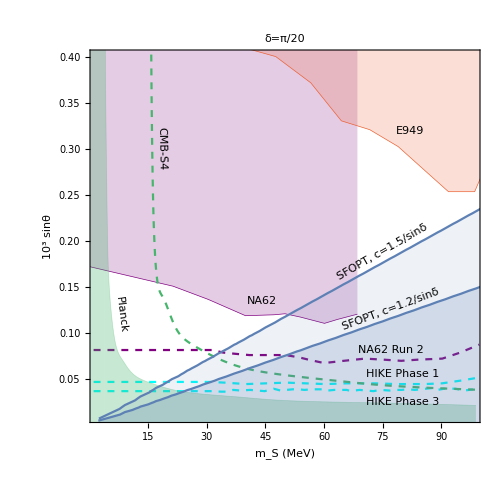

```mathematica
Show[Kaondecay1,Kaondecay2,CMB‵perspect,Planck,c12‵δpi20‵MeV‵strength‵plot,c15‵δpi20‵MeV‵strength‵plot,PlotRange->{{2,98},{0.01,0.4}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["m_S (MeV)",FontFamily->"Times",FontSize->24],Style["10^3 sinθ",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,AspectRatio->1,PlotLabel->Style["δ=π/20",FontFamily->"Times",FontSize->26],Epilog->{Inset[Framed[Style["NA62",Purple, FontFamily->"Times",FontSize->24],FrameStyle->None],{44,0.135}],Inset[Rotate[Framed[Style["SFOPT, c=1.2/sinδ",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],20.5Degree],{77,0.125}],Inset[Rotate[Framed[Style["SFOPT, c=1.5/sinδ",ColorData[97,1],FontFamily->"Times",FontSize->24],FrameStyle->None],30Degree],{75,0.188}],Inset[Rotate[Framed[Style["Planck",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-83 Degree],{8,0.12}],Inset[Rotate[Framed[Style["CMB-S4",ColorData[97,15],FontFamily->"Times",FontSize->24],FrameStyle->None],-89Degree],{18.5,0.3}],Inset[Rotate[Framed[Style["NA62 Run 2",Purple,FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{77,0.081}],Inset[Rotate[Framed[Style["HIKE Phase 1",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{80,0.055}],Inset[Rotate[Framed[Style["HIKE Phase 3",Darker[Cyan],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{80,0.024}],Inset[Rotate[Framed[Style["E949",ColorData[97,4],FontFamily->"Times",FontSize->24],FrameStyle->None],0Degree],{82,0.32}]}]
```